```mathematica
Series[Exp[z],{z,0,10}]
```

1+z+z^2/2+z^3/6+z^4/24+z^5/120+z^6/720+z^7/5040+z^8/40320+z^9/362880+z^10/3628800+O[z]^11

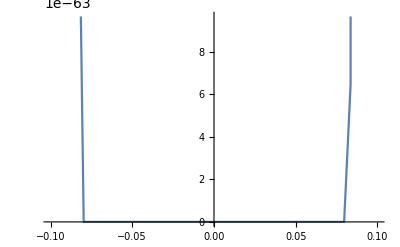

(2 ⅇ^(-1/z^2))/z^3

```mathematica
Plot[Exp[-1/z^2],{z,-0.1,0.1}]
D[Exp[-1/z^2],{z}]
```

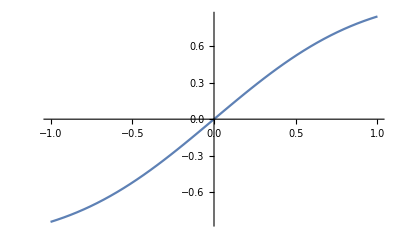

(-1)^Floor[(π+2 Arg[z])/(2 π)]+ⅇ^(-1/z^2) (-z/(√π)+z^3/(2 √π)-(3 z^5)/(4 √π)+(15 z^7)/(8 √π)-(105 z^9)/(16 √π)+O[z]^11)

0

```mathematica
Plot[Erf[z],{z,-1,1}]
Series[Erf[1/z],{z,0,10}]

Limit[D[Erf[1/z],{z}],z->0]
```

```mathematica
cdf[x_,σ_]:= 1/2(1+Erf[x/(σ √2)]);

With[{x=1},
Series[cdf[x,σ],{σ,0,10}]]//Normal


With[{x=1},
Series[cdf[x,σ],{σ,0.5,10}]]//Normal
```

1/2 ⅇ^(-1/(2 σ^2)) (ⅇ^(1/(2 σ^2))+(-1)^Floor[(π+2 Arg[σ])/(2 π)] ⅇ^(1/(2 σ^2))-√(2/π) σ+√(2/π) σ^3-3 √(2/π) σ^5+15 √(2/π) σ^7-105 √(2/π) σ^9)

0.97725-0.215964 (-0.5+σ)-0.431928 (-0.5+σ)^2+0.863855 (-0.5+σ)^3+0.575904 (-0.5+σ)^4-5.75904 (-0.5+σ)^5+12.4395 (-0.5+σ)^6-4.51947 (-0.5+σ)^7-58.5337 (-0.5+σ)^8+227.758 (-0.5+σ)^9-459.338 (-0.5+σ)^10

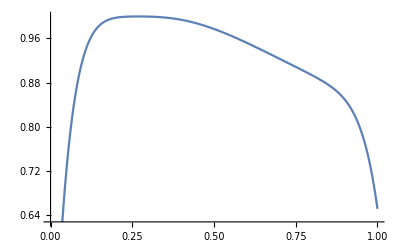

```mathematica
Plot[%59,{σ,0,1}]
```

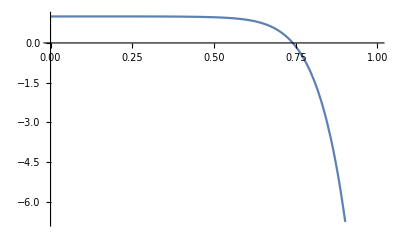

```mathematica
Plot[1/2 ⅇ^(-1/(2 σ^2)) (ⅇ^(1/(2 σ^2))+(-1)^Floor[(π+2 Arg[σ])/(2 π)] ⅇ^(1/(2 σ^2))-√(2/π) σ+√(2/π) σ^3-3 √(2/π) σ^5+15 √(2/π) σ^7-105 √(2/π) σ^9),{σ,0,1}]
```

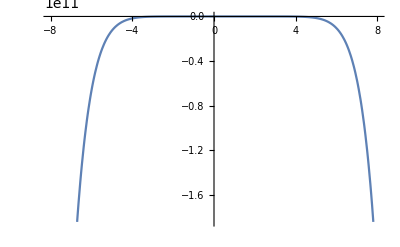

```mathematica
Plot[%45,{σ,-8,8}]
```

```mathematica
Table[Limit[D[cdf[z-1/z],{z,n}],z->0],{n,1,8,1}]
```

{0,0,0,0,0,0,0,0}

```mathematica
BSFormula[S_,lo_,Z_]:=S/2*(1-Exp[-lo])+S/2(Erf[(lo/Z+Z/2)/(√2)]-Exp[-lo]*Erf[(lo/Z-Z/2)/(√2)]);
```

```mathematica
Series[BSFormula[S,lo,Z],{Z,1,5}]//TraditionalForm
```

1/2 ⅇ^-lo S (erf(1/(2 √2)-lo/(√2))+ⅇ^lo erf(lo/(√2)+1/(2 √2))+ⅇ^lo-1)+1/2 ((ⅇ^(-1/8 (1-2 lo)^2-lo) (2 lo+1))/(√(2 π))+(2 ⅇ^(-1/8 (2 lo+1)^2) (1/(2 √2)-lo/(√2)))/(√π)) S (Z-1)+1/2 ((ⅇ^(-1/8 (1-2 lo)^2-lo) (8 lo^3+4 lo^2-18 lo-1))/(8 √(2 π))+(2 ((ⅇ^(-1/8 (2 lo+1)^2) lo)/(√2)-(ⅇ^(-1/8 (2 lo+1)^2) (2 lo+1) (1/(2 √2)-lo/(√2))^2)/(2 √2)))/(√π)) S (Z-1)^2+1/2 ((2 (1/12 ⅇ^(-1/8 (2 lo+1)^2) (4 lo^2+4 lo-3) (1/(2 √2)-lo/(√2))^3-1/2 ⅇ^(-1/8 (2 lo+1)^2) lo (2 lo+1) (1/(2 √2)-lo/(√2))-(ⅇ^(-1/8 (2 lo+1)^2) lo)/(√2)))/(√π)+(ⅇ^(-1/8 (1-2 lo)^2-lo) (32 lo^5+16 lo^4-240 lo^3-56 lo^2+218 lo-3))/(96 √(2 π))) S (Z-1)^3+1/2 (1/(√π)2 (-(ⅇ^(-1/8 (2 lo+1)^2) (2 lo+1) (4 lo^2+4 lo-11) (1/(2 √2)-lo/(√2))^4)/(48 √2)+(ⅇ^(-1/8 (2 lo+1)^2) (2 lo+1) (√2 lo (1/(2 √2)-lo/(√2))-lo^2/2))/(2 √2)+1/12 ⅇ^(-1/8 (2 lo+1)^2) (4 lo^2+4 lo-3) (√2 lo (1/(2 √2)-lo/(√2))^2+(lo (1/(2 √2)-lo/(√2))^2)/(√2))+(ⅇ^(-1/8 (2 lo+1)^2) lo)/(√2))+(ⅇ^(-1/8 (1-2 lo)^2-lo) (128 lo^7+64 lo^6-2016 lo^5-624 lo^4+6744 lo^3+876 lo^2-3482 lo+11))/(1536 √(2 π))) S (Z-1)^4+1/2 (1/(√π)2 ((ⅇ^(-1/8 (2 lo+1)^2) (2 lo+1) (lo^2-√2 lo (1/(2 √2)-lo/(√2))))/(2 √2)+1/12 ⅇ^(-1/8 (2 lo+1)^2) (4 lo^2+4 lo-3) ((1/(2 √2)-lo/(√2)) lo^2+(1/(2 √2)-lo/(√2)) (lo^2/2-√2 lo (1/(2 √2)-lo/(√2)))-((1/(2 √2)-lo/(√2))^2 lo)/(√2))+(ⅇ^(-1/8 (2 lo+1)^2) (2 lo+1) (4 lo^2+4 lo-11) (-(lo (1/(2 √2)-lo/(√2))^3)/(√2)-(√2 lo (1/(2 √2)-lo/(√2))^2+(lo (1/(2 √2)-lo/(√2))^2)/(√2)) (1/(2 √2)-lo/(√2))))/(48 √2)+1/480 ⅇ^(-1/8 (2 lo+1)^2) (16 lo^4+32 lo^3-72 lo^2-88 lo+25) (1/(2 √2)-lo/(√2))^5-(ⅇ^(-1/8 (2 lo+1)^2) lo)/(√2))+(ⅇ^(-1/8 (1-2 lo)^2-lo) (512 lo^9+256 lo^8-13824 lo^7-4864 lo^6+100800 lo^5+21216 lo^4-204512 lo^3-17392 lo^2+69618 lo+25))/(30720 √(2 π))) S (Z-1)^5+O((Z-1)^6)